```mathematica
λ=3;a=1;x0=20.;ν=1.;tmax=1000.;nxy=33;

data=Reap[
sol=NDSolveValue[{D[u[t,x],t]+λ D[u[t,x],x,x,x,x]+ν D[u[t,x],x,x]+u[t,x]D[u[t,x],x]==0,u[0,x]==ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2) ,u[t,-x0]==u[t,x0]},u,{t,0,tmax},{x,-x0,x0},Method->"StiffnessSwitching","MethodMonitor":>(Sow[NDSolve`Self[[0]]];)];];
```

```mathematica
ndivs=100;
tval=tmax;
err=Table[D[sol[tt, xx], {tt}] + sol[tt, xx]*D[sol[tt, xx], {xx}] +ν D[sol[tt, xx], {xx, 2}] + λ D[sol[tt, xx], {xx, 4}]/.{xx->0,tt->τ} ,{τ,0,tval,tval/ndivs}];
```

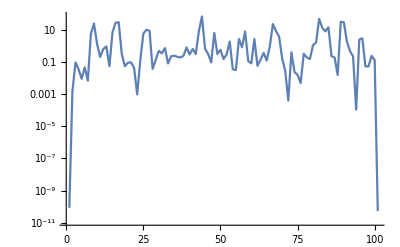

```mathematica
ListLogPlot[Abs[err],Joined->True]
```

```mathematica
data//Last
```

{{NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`ExplicitModifiedMidpoint,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`StiffnessSwitching,NDSolve`Extrapolation,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler,NDSolve`LinearlyImplicitEuler}}